This code has been taken from
https://mathematica.stackexchange.com/questions/170268/how-to-generate-all-feynman-diagrams-with-mathematica

```mathematica
ClearAll[Δ,corr,reduce,allgraphs]
SetAttributes[Δ,Orderless];

corr[{a_,b_}]:=Δ[a,b];
corr[{a_,b__}]:=corr[{a,b}]=Sum[corr[{a,List[b][[i]]}] corr[Flatten@{List[b][[;;i-1]],List[b][[i+1;;]]}],{i,1,Length[List[b]]}];

reduce[permutations_][graphs_List]/;Length[graphs]==1:={{First[graphs],1}};
reduce[permutations_][graphs_List]:=Map[MapAt[First,1],Tally[(#/. permutations)&/@graphs,ContainsAny],{1}]
```

```mathematica
allgraphs[n_List]/;OddQ[Sum[i n[[i]],{i,1,Length[n]}]]:={}
allgraphs[{2,0...}]={{{1<->2},2}};
allgraphs[n_List]:=Block[{permutations,gathered,removeiso,coeff},permutations=Dispatch[Thread/@Thread[ConstantArray[Range[n[[1]]+1,Total[n]],(Total[n]-n[[1]])!]->Permutations[Range[n[[1]]+1,Total[n]]]]/. Rule[a_,a_]->Nothing];
gathered=GatherBy[Select[{Expand[corr[Flatten[Table[ConstantArray[Total[n[[;;i-1]]]+j+1,i],{i,1,Length[n]},{j,0,n[[i]]-1}]]]]/. Plus->Sequence},WeaklyConnectedGraphQ[Graph[{#}/. {Times[a_Integer,g__]:>g,Times->Sequence}/. Power[a_,b_]:>Sequence@@ConstantArray[a,b]/. Δ->UndirectedEdge]]&],If[Head[First[#]]===Integer,First[#],1]&];
coeff=Map[If[Head[#[[1,1]]]===Integer,#[[1,1]],1]&,gathered];
removeiso=reduce[permutations]/@(Map[Sequence@@{#/. Times->Δ/.  Power[a_,b_]:>Sequence@@ConstantArray[a,b]}&,(gathered/coeff),{2}]);
Flatten[Table[Map[{(List@@#[[1]])/. Δ->UndirectedEdge,Apply[Times,Rest[n]!] Apply[Times,(Range[Length[n]]!)^n]/(#[[2]] coeff[[j]])}&,removeiso[[j]],{1}],{j,1,Length[coeff]}],1]]
```

```mathematica
allgraphsplot[n_]:=Graph[First[#],PlotLabel->Last[#],VertexLabels->Thread[Range[n[[1]]]->Range[n[[1]]]]]&/@allgraphs[n]
```

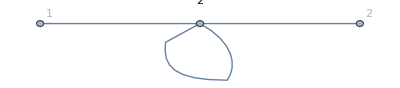

```mathematica
allgraphsplot[{2,0,0,1}]
```

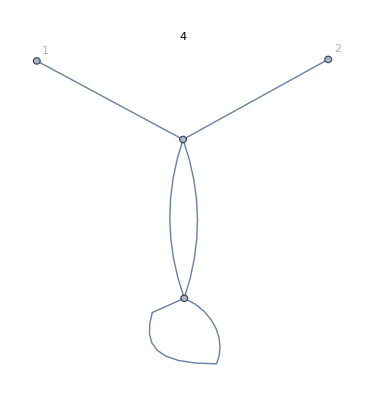
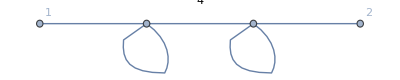
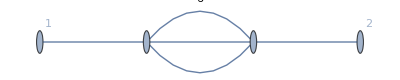

```mathematica
allgraphsplot[{2,0,0,2}]
```

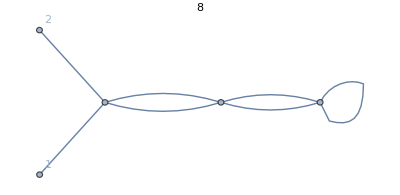
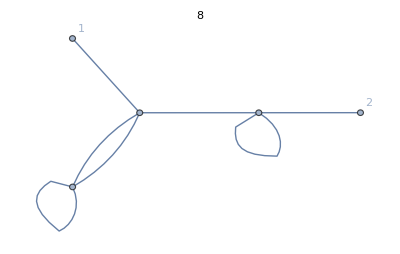
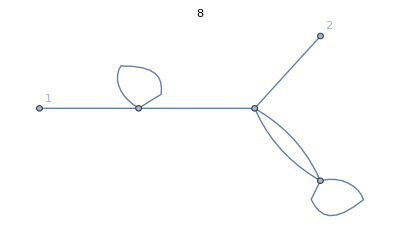
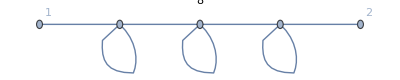
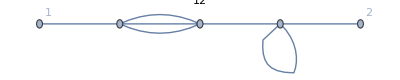
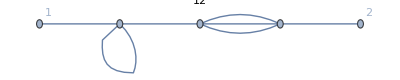
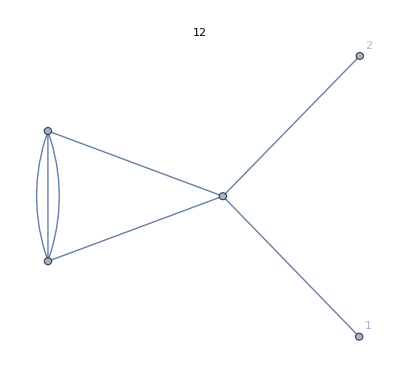
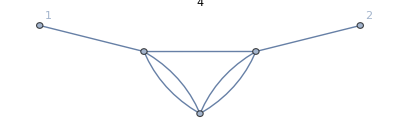

```mathematica
allgraphsplot[{2,0,0,3}]
```

```mathematica
allgraphs[{0,0,2}]
```

{{{1,2},4},{{1<->1,1<->2,2<->2},8}}

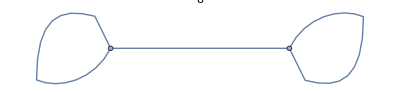
{Graph[{1,2},PlotLabel→4,VertexLabels→{}],-Graphics-}

```mathematica
allgraphsplot[{0,0,2}]
```